# nearest neighbor algorithm

## входные данные

### поле:

```mathematica
rows=40;
columns=60;
```

### дроны:

```mathematica
numberOfDrones=3;
turnsOfDrones=112993;
capacityOfDrones = 200;
```

### продукты:

```mathematica
numberOfProducts=5;
productsWeights = RandomInteger[{1,capacityOfDrones},numberOfProducts];
maxNumberOfProductsInWarehouses=100;
```

### склады:

```mathematica
numberOfWarehouses = 3;
```

```mathematica
Clear@generateWarehousesCoords
generateWarehousesCoords[rows_Integer,columns_Integer,number_Integer]:=
Module[
{coords=Thread[{RandomInteger[columns,number],RandomInteger[rows,number]}]},

While[ !DuplicateFreeQ[coords],
coords=Thread[{RandomInteger[columns,number],RandomInteger[rows,number]}]
];
coords
]
```

```mathematica
warehousesCoords=generateWarehousesCoords[rows,columns,numberOfWarehouses]
```

{{18,17},{60,4},{25,32}}

```mathematica
productsInWarehouses=RandomInteger[maxNumberOfProductsInWarehouses,{numberOfWarehouses,numberOfProducts}]
```

{{92,75,58,36,34},{3,39,14,10,50},{84,80,92,44,57}}

```mathematica
totalNumberOfProducts=Total@productsInWarehouses
```

{179,194,164,90,141}

### заказы:

```mathematica
numberOfOrders =10;
```

```mathematica
Clear@generateOrdersCoords
generateOrdersCoords[rows_Integer,columns_Integer,number_Integer,warehouses:{{_Integer,_Integer}..}]:=
Module[
{coords=Thread[{RandomInteger[columns,number],RandomInteger[rows,number]}]},

While[ !DuplicateFreeQ[coords~Join~warehousesCoords],
coords=Thread[{RandomInteger[columns,number],RandomInteger[rows,number]}]
];
coords
]
```

```mathematica
ordersCoords=generateOrdersCoords[rows,columns,numberOfOrders,warehousesCoords]
```

{{46,33},{46,16},{42,1},{48,37},{56,25},{17,10},{12,29},{28,16},{18,25},{25,29}}

```mathematica
Floor[Mean@totalNumberOfProducts/numberOfOrders]
```

15

```mathematica
Clear@generateOrders
generateOrders[numberOfOrders_Integer,totalNumberOfProducts_List]:=
RandomInteger[
Min[Floor[Mean@totalNumberOfProducts/numberOfOrders],3],
{numberOfOrders,Length@totalNumberOfProducts}
]
```

```mathematica
orders=generateOrders[numberOfOrders,totalNumberOfProducts]
```

{{0,1,1,1,2},{0,0,1,2,1},{2,2,0,3,2},{1,3,2,3,3},{0,2,1,1,2},{1,3,1,0,2},{1,2,3,1,3},{0,1,1,1,1},{3,0,3,0,3},{1,2,3,1,0}}

```mathematica
And@@(#>0&/@(totalNumberOfProducts-Total@orders))
```

True

### база данных:

```mathematica
data=<|
"area"-> <|
"rows"->rows,
"columns"->columns
|>,

"drones"-><|
"number"->numberOfDrones,
"turns"->turnsOfDrones,
"capacity"->capacityOfDrones,
"drone"->AssociationThread[Range@numberOfDrones->(<|"coords"->#⟦1⟧,"products"->#⟦2⟧,"score"->#⟦3⟧|>&/@Thread[{ConstantArray[warehousesCoords⟦1⟧,numberOfDrones],ConstantArray[0,{numberOfDrones,numberOfProducts}],ConstantArray[0,numberOfDrones]}])],
"coords"->ConstantArray[warehousesCoords⟦1⟧,numberOfDrones],
"products"->ConstantArray[0,{numberOfDrones,numberOfProducts}],
"score"->ConstantArray[0,numberOfDrones]
|>,

"products"-><|
"number"->numberOfProducts,
"weights"->productsWeights
|>,

"warehouses"-><|
"number"->numberOfWarehouses,
"warehouse"->AssociationThread[Range@numberOfWarehouses->(<|"coords"->#⟦1⟧,"products"->#⟦2⟧|>&/@Thread[{warehousesCoords,productsInWarehouses}])]
|>,

"orders"-><|
"number"->numberOfOrders,
"order"->AssociationThread[Range@numberOfOrders->(<|"coords"->#⟦1⟧,"list"->#⟦2⟧|>&/@Thread[{ordersCoords,orders}])],
"mask"->ConstantArray[0,numberOfOrders]
|>
|>;
```

## анализ данных

```mathematica
data⟦"warehouses","warehouse",All,"coords"⟧
```

<|1→{18,17},2→{60,4},3→{25,32}|>

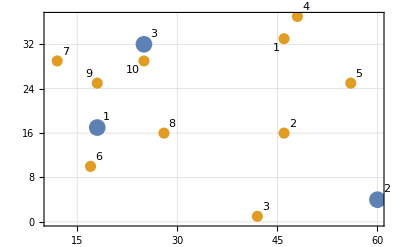

```mathematica
plot=ListPlot[{MapThread[Labeled,{Values@data⟦"warehouses","warehouse",All,"coords"⟧,Range@data["warehouses","number"]}],MapThread[Labeled,{Values@data⟦"orders","order",All,"coords"⟧,
Range@data["orders","number"]}]},PlotTheme->"Detailed",PlotStyle->{PointSize[0.03],PointSize[0.02]}]
```

3 склада, расположенные в точках:

```mathematica
Values@data⟦"warehouses","warehouse",All,"coords"⟧//Column
```

{18,17}
{60,4}
{25,32}

где первый склад - начальный, то есть откуда стартуют дроны. Есть 5 типов продуктов, которые весят соответственно:

```mathematica
data["products","weights"]//Column
```

49
156
162
111
190

каждого продукта на каждом складе соответственно:

```mathematica
Values@data⟦"warehouses","warehouse",All,"products"⟧//Column
```

{92,75,58,36,34}
{3,39,14,10,50}
{84,80,92,44,57}

3 дрона, каждый из которых находится в первом складе и имеет грузоподъемность:

```mathematica
data["drones","capacity"]
```

200

необходимо доставить 10 заказов на данные точки:

```mathematica
Values@data⟦"orders","order",All,"coords"⟧//Column
```

{46,33}
{46,16}
{42,1}
{48,37}
{56,25}
{17,10}
{12,29}
{28,16}
{18,25}
{25,29}

каждому клиенту необходимо соответсвующих товаров:

```mathematica
Values@data⟦"orders","order",All,"list"⟧//Column
```

{0,1,1,1,2}
{0,0,1,2,1}
{2,2,0,3,2}
{1,3,2,3,3}
{0,2,1,1,2}
{1,3,1,0,2}
{1,2,3,1,3}
{0,1,1,1,1}
{3,0,3,0,3}
{1,2,3,1,0}

## алгоритм

Для каждого дрона определяем ближайший склад, где можно пополнить запас продуктов, а также ближайшего клиента от этого склада.  Среди всех дронов выбираем того, у которого сумма длин двух расстояний наименьшая и выполняем им весь заказ или его часть. Так до тех пор, пока все заказы не будут выполнены.

```mathematica
plot
```

-Graphics-

```mathematica
(*нужно сделать проверку, чтобы дрон выбирал склад только в том случае, если на нем есть хотя бы один нужный товар*)
```

```mathematica
Clear@chooseShortestPath
chooseShortestPath[droneCoords_,data_Association]:=
Module[
{to,from,warehouses},
warehouses=Values@data⟦"warehouses","warehouse",All,"coords"⟧;
to=MinimalBy[warehouses,N@EuclideanDistance[#,droneCoords]&];

from=MinimalBy[
Pick[Values@data⟦"orders","order",All,"coords"⟧,data["orders","mask"],0],
N@EuclideanDistance[to⟦1⟧,#]&];

{{Position[warehouses, to⟦1⟧]⟦1,1⟧,to⟦1⟧},{Position[Values@data⟦"orders","order",All,"coords"⟧, from⟦1⟧]⟦1,1⟧,from⟦1⟧},
Ceiling@EuclideanDistance[droneCoords,to⟦1⟧]+Ceiling@EuclideanDistance[to⟦1⟧,from⟦1⟧]}
]
```

```mathematica
Clear@loadProducts
loadProducts[data_Association,warehouseID_Integer,orderID_Integer,droneID_Integer]:=
Module[
{tempData=data,capacity =data["drones","capacity"],weights=data["products","weights"],numberOfProduct},
Do[
numberOfProduct=
Min[
data⟦"warehouses","warehouse",warehouseID,"products",i⟧,
data⟦"orders","order",orderID,"list",i⟧,
Quotient[capacity,weights⟦i⟧]
];
tempData⟦"warehouses","warehouse",warehouseID,"products",i⟧-=numberOfProduct;
tempData⟦"drones","drone",droneID,"products",i⟧+=numberOfProduct;
capacity-=weights⟦i⟧ numberOfProduct;

(*If[numberOfProduct>0,
Print["дрон ",droneID," загрузил ",numberOfProduct, " у.е. продукта ", i, " со склада ",warehouseID," для заказа ", orderID]];*)

If[capacity≤0,Break[]]
,{i,Length@weights}];
tempData
]
```

```mathematica
Clear@unloadProduct
unloadProduct[data_Association,orderID_Integer,droneID_Integer]:=
Module[
{tempData=data},
tempData⟦"orders","order",orderID,"list"⟧-=tempData⟦"drones","drone",droneID,"products"⟧;
tempData⟦"drones","drone",droneID,"products"⟧=ConstantArray[0,data["products","number"]];
(*Print["дрон ",droneID, " отгрузил товар клиенту ", orderID];*)
If[DeleteDuplicates@tempData⟦"orders","order",orderID,"list"⟧=={0},tempData⟦"orders","mask",orderID⟧=1;Print["заказ ",orderID, " полностью выполнен"]];
tempData
]
```

```mathematica
-Graphics-;
```

```mathematica
plot
```

-Graphics-

```mathematica
x=RandomInteger[50,{5,2}]
```

{{49,34},{43,32},{8,50},{10,32},{42,39}}

```mathematica
MinimalBy[x,Last@chooseShortestPath[#,data]&]⟦1⟧
```

{10,32}

```mathematica
FirstPosition[x,%]
```

{4}

```mathematica
RandomChoice[Last@chooseShortestPath[#,data]&/@x]
```

21

```mathematica
Association
```

```mathematica
Clear@solve
solve[data_Association]:=
Module[
{nextDrone,droneID,nextWarehouse,nextOrder,score,tempData=data},
While[
Times@@tempData["orders","mask"]≠1,

(*выбор дрона*)
nextDrone=RandomChoice[MinimalBy[Values@tempData⟦"drones","drone",All,"coords"⟧,Last@chooseShortestPath[#,tempData]&]];
droneID=RandomChoice[Position[Values@tempData⟦"drones","drone",All,"coords"⟧,nextDrone]]⟦1⟧;
{nextWarehouse,nextOrder,score}=chooseShortestPath[tempData["drones","drone",droneID,"coords"],tempData];
(*Print["выбран дрон ",droneID];*)

(*перемещение дрона на ближайший склад*)
tempData["drones","drone",droneID,"coords"]=nextWarehouse⟦2⟧;
(*Print["дрон ",droneID," переместился к складу ",nextWarehouse⟦1⟧," с координатами ",nextWarehouse⟦2⟧];*)

(*погрузка товара*)
tempData=loadProducts[tempData,nextWarehouse⟦1⟧,nextOrder⟦1⟧,droneID];

(*перемещаение дрона к ближайшему клиенту*)
tempData["drones","drone",droneID,"score"]+=score;
tempData["drones","drone",droneID,"coords"]=nextOrder⟦2⟧;
(*Print["дрон ",droneID," переместился к клиенту ",nextOrder⟦1⟧," с координатами ",nextOrder⟦2⟧];*)

(*разгрузка товара*)
tempData=unloadProduct[tempData,nextOrder⟦1⟧,droneID]
];
tempData
]
```

```mathematica
plot
```

-Graphics-

```mathematica
solution=solve[data];
```

заказ 6 полностью выполнен

заказ 9 полностью выполнен

заказ 8 полностью выполнен

заказ 10 полностью выполнен

заказ 7 полностью выполнен

заказ 1 полностью выполнен

заказ 4 полностью выполнен

заказ 3 полностью выполнен

заказ 2 полностью выполнен

заказ 5 полностью выполнен

```mathematica
solution⟦"drones","drone"⟧
```

<|1→<|coords→{48,37},products→{0,0,0,0,0},score→404|>,2→<|coords→{48,37},products→{0,0,0,0,0},score→434|>,3→<|coords→{56,25},products→{0,0,0,0,0},score→1168|>|>